FittedModel[8.26556-2.41777×10^-7 x^2]

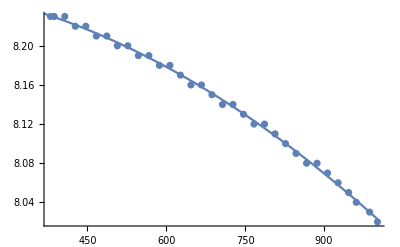

```mathematica
data1= {{380,8.23},{387.1,8.23},{407.1,8.23},{427.1,8.22},{447.1,8.22},{467.1,8.21}, {487.1,8.21},{507.1,8.20},{527.1,8.20},{547.1,8.19},{567.1,8.19}, {587.1,8.18},{607.1,8.18},{627.1,8.17},{647.1,8.16},{667.1,8.16},{687.1,8.15},{707.1,8.14},{727.1,8.14},{747.1,8.13},{767.1,8.12},{787.1,8.12},{807.1,8.11},{827.1,8.10},{847.1,8.09},{867.1,8.08},{887.1,8.08},{907.1,8.07},{927.1,8.06},{947.1,8.05},{961.7,8.04},{987.1,8.03},{1002.0,8.02}};
nlm1=NonlinearModelFit[data1, a^2 -b^2 x^2,{a,b},x]
Show[ListPlot[data1],Plot[nlm1[x],{x,0,1002.0}]]
```

FittedModel[8.27407-2.48694×10^-7 x^2]

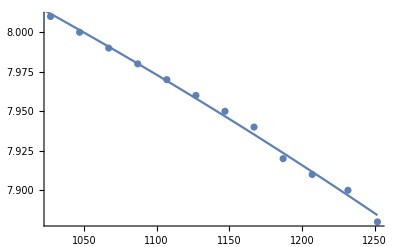

```mathematica
data2 = {{1027.1,8.01},{1047.1,8.00},{1067.1,7.99},{1087.1,7.98},{1107.1,7.97},{1127.1,7.96},{1147.1,7.95},{1167.1,7.94},{1187.1,7.92},{1207.1,7.91},{1231.7,7.90},{1252.0,7.88}};
nlm2=NonlinearModelFit[data2, a^2 -b^2 x^2,{a,b},x]
Show[ListPlot[data2],Plot[nlm2[x],{x,1002.0,1252.0}]]
```

FittedModel[8.26592-2.42455×10^-7 x^2]

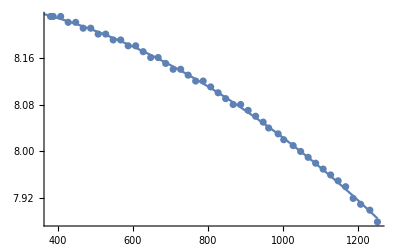

```mathematica
data12 = {{380,8.23},{387.1,8.23},{407.1,8.23},{427.1,8.22},{447.1,8.22},{467.1,8.21}, {487.1,8.21},{507.1,8.20},{527.1,8.20},{547.1,8.19},{567.1,8.19}, {587.1,8.18},{607.1,8.18},{627.1,8.17},{647.1,8.16},{667.1,8.16},{687.1,8.15},{707.1,8.14},{727.1,8.14},{747.1,8.13},{767.1,8.12},{787.1,8.12},{807.1,8.11},{827.1,8.10},{847.1,8.09},{867.1,8.08},{887.1,8.08},{907.1,8.07},{927.1,8.06},{947.1,8.05},{961.7,8.04},{987.1,8.03},{1002.0,8.02},{1027.1,8.01},{1047.1,8.00},{1067.1,7.99},{1087.1,7.98},{1107.1,7.97},{1127.1,7.96},{1147.1,7.95},{1167.1,7.94},{1187.1,7.92},{1207.1,7.91},{1231.7,7.90},{1252.0,7.88}};
nlm12=NonlinearModelFit[data12, a^2 -b^2 x^2,{a,b},x]
Show[ListPlot[data12],Plot[nlm12[x],{x,0,1252.0}]]
```

FittedModel[8.26955-2.47679×10^-7 x^2]

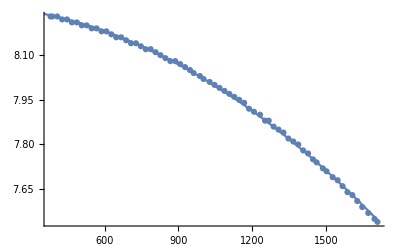

```mathematica
data123 ={{380,8.23},{387.1,8.23},{407.1,8.23},{427.1,8.22},{447.1,8.22},{467.1,8.21}, {487.1,8.21},{507.1,8.20},{527.1,8.20},{547.1,8.19},{567.1,8.19}, {587.1,8.18},{607.1,8.18},{627.1,8.17},{647.1,8.16},{667.1,8.16},{687.1,8.15},{707.1,8.14},{727.1,8.14},{747.1,8.13},{767.1,8.12},{787.1,8.12},{807.1,8.11},{827.1,8.10},{847.1,8.09},{867.1,8.08},{887.1,8.08},{907.1,8.07},{927.1,8.06},{947.1,8.05},{961.7,8.04},{987.1,8.03},{1002.0,8.02},{1027.1,8.01},{1047.1,8.00},{1067.1,7.99},{1087.1,7.98},{1107.1,7.97},{1127.1,7.96},{1147.1,7.95},{1167.1,7.94},{1187.1,7.92},{1207.1,7.91},{1231.7,7.90},{1252.0,7.88},{1267.1,7.88},{1287.1,7.86},{1307.1,7.85},{1327.1,7.84},{1347.1,7.82},{1367.1,7.81},{1387.1,7.80},{1407.1,7.78},{1427.1,7.77},{1447.1,7.75},{1461.7,7.74},{1487.1,7.72},{1502.0,7.71},{1527.1,7.69},{1547.1,7.68},{1567.1,7.66},{1587.1,7.64},{1607.1,7.63},{1627.1,7.61},{1647.1,7.59},{1671.7,7.57},{1697.1,7.55},{1709.1,7.54}};
nlm123=NonlinearModelFit[data123, a^2 -b^2 x^2,{a,b},x]
Show[ListPlot[data123],Plot[nlm123[x],{x,0,1709.1}]]
```

```mathematica
(*Density*)
dataρ ={{1737.1,2.600},{1736.1,2.600},{1736.1,2.762},{ 1725.1,2.762},{ 1725.1,2.762},{ 1709.1,2.762},{ 1697.1,2.762},{ 1697.1,3.314},{ 1671.7,3.318},{ 1647.1,3.322},{ 1627.1,3.325},{ 1607.1,3.329},{ 1587.1,3.332},{ 1567.1,3.335},{ 1547.1,3.338},{ 1527.1,3.341},{ 1502.0,3.344},{ 1487.1,3.346},{ 1461.7,3.350},{ 1447.1,3.352},{ 1427.1,3.355},{ 1407.1,3.357},{ 1387.1,3.360},{ 1367.1,3.363},{ 1347.1,3.365},{ 1327.1,3.368},{ 1307.1,3.370},{ 1287.1,3.373},{ 1267.1,3.375},{ 1252.0 ,3.377},{1231.7 ,3.379},{1207.1 ,3.382},{1187.1 ,3.384},{1167.1 ,3.386},{1147.1 ,3.388},{1127.1 ,3.391},{1107.1 ,3.393},{1087.1 ,3.395},{1067.1 ,3.397},{1047.1 ,3.398},{1027.1 ,3.400},{1002.0 ,3.403},{987.1,3.404},{ 961.7,3.406},{ 947.1,3.408},{ 927.1 ,3.409},{907.1 ,3.411},{887.1 ,3.413},{867.1 ,3.414},{847.1 ,3.416},{827.1 ,3.417},{807.1 ,3.419},{787.1 ,3.420},{767.1 ,3.421},{747.1 ,3.423},{727.1 ,3.424},{707.1 ,3.425},{687.1 ,3.427},{667.1 ,3.428},{647.1 ,3.429},{627.1 ,3.430},{607.1 ,3.431},{587.1 ,3.433},{567.1 ,3.434},{547.1 ,3.435},{527.1 ,3.436},{507.1 ,3.437},{487.1 ,},{467.1 ,},{447.1 ,},{427.1},{407.1,},{387.1,},{380.0,}}
```